```mathematica
mySqrt[X_]=-I*Sqrt[-X];
```

```mathematica
G := Inverse[{{z-J-q*Cos[k],-q*Cos[k]},{-q*Cos[k],-z-J-q*Cos[k]}}-c*(p/4*(Cos[k]-1)*Inverse[{{1-p/4(1/(2J*q)-(J^2-z^2)/(2J*q*a)-1/a)(z+J),(z-J)p/4(1/(2J*q)-(J^2-z^2)/(2J*q*a)-1/a)},{-(z+J)p/4(1/(2J*q)-(J^2-z^2)/(2J*q*a)-1/a),1+(z-J)p/4(1/(2J*q)-(J^2-z^2)/(2J*q*a)-1/a)}}].{{1,1},{1,1}}+p/4*(1+Cos[k])*Inverse[{{1-p/4(1/(2J*q)-(J^2-z^2)/(2J*q*a)+1/a)(z+J),(z-J)p/4(1/(2J*q)-(J^2-z^2)/(2J*q*a)+1/a)},{-(z+J)p/4(1/(2J*q)-(J^2-z^2)/(2J*q*a)+1/a),1+(z-J)p/4(1/(2J*q)-(J^2-z^2)/(2J*q*a)+1/a)}}].{{1,1},{1,1}})]
```

```mathematica
G1 = G/.{a->mySqrt[(J^2-z^2)^2-(2*J*q)^2]}
```

{{(-J-z-q Cos[k]-c (1/4 p (-(p (-J-z) (1/(2 J q)-ⅈ/(√(4 J^2 q^2-1^2))-(ⅈ (J^2-z^2))/(2 J q √(4 J^2 q^2-1^2))))/(4 (1-p/(4 q)+(ⅈ J p)/(2 √1)+(ⅈ J^2 p)/(4 q √1)-(ⅈ p z^2)/(4 q √(4 J^2 q^2-1^2))))+(1-1/4 p 1 (1))/1) (-1+Cos[k])+1/4 p (-1/(4 1)+1) (1+Cos[k])))/(-((-q Cos[k]-c (1/4 p (-(p (-J+z) (1/(2 J q)-ⅈ/(√(1-1))-(ⅈ (J^2-z^2))/(2 J q 1)))/(4 (1-p/(4 q)+(ⅈ J p)/(2 1)+(ⅈ J^2 p)/1-(ⅈ p z^2)/(4 q √(1-1))))+(1+1)/1) (-1+Cos[k])+1/4 p (-1/1+1) (1+Cos[k]))) (-q Cos[k]-c 1))+(1) 1),(q 1+1)/(-(1)+1)},{1}}
 |  |  |  |

```mathematica
Gf := G1/.{c->0.01,p->0.5,J->1,q->0.1,z->z+I*n}
```

```mathematica
Gfinall = Part[Gf,1,1]/.{n->0.006}
```

((-1.-0.006 ⅈ)-z-0.1 Cos[k]-0.01 (0.125 (-(0.125 ((-1.-0.006 ⅈ)-z) (5.-ⅈ/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))-((0.+5. ⅈ) (1-((0.+0.006 ⅈ)+z)^2))/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))))/(-0.25+(0.+1.5 ⅈ)/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))-((0.+1.25 ⅈ) ((0.+0.006 ⅈ)+z)^2)/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2)))+(1-0.125 ((1.+0.006 ⅈ)+z) (5.-ⅈ/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))-((0.+5. ⅈ) (1-((0.+0.006 ⅈ)+z)^2))/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))))/(-0.25+(0.+1.5 ⅈ)/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))-((0.+1.25 ⅈ) ((0.+0.006 ⅈ)+z)^2)/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2)))) (-1+Cos[k])+0.125 (-(0.125 ((-1.-0.006 ⅈ)-z) (5.+ⅈ/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))-((0.+5. ⅈ) (1-((0.+0.006 ⅈ)+z)^2))/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))))/(-0.25+(0.+1. ⅈ)/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))-((0.+1.25 ⅈ) ((0.+0.006 ⅈ)+z)^2)/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2)))+(1-0.125 ((1.+0.006 ⅈ)+z) (5.+ⅈ/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))-((0.+5. ⅈ) (1-((0.+0.006 ⅈ)+z)^2))/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))))/(-0.25+(0.+1. ⅈ)/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))-((0.+1.25 ⅈ) ((0.+0.006 ⅈ)+z)^2)/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2)))) (1+Cos[k])))/(-((-0.1 Cos[k]-0.01 (0.125 (-(0.125 ((-1.+0.006 ⅈ)+z) (5.-ⅈ/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))-((0.+5. ⅈ) (1-((0.+0.006 ⅈ)+z)^2))/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))))/(-0.25+(0.+1.5 ⅈ)/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))-((0.+1.25 ⅈ) ((0.+0.006 ⅈ)+z)^2)/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2)))+(1+0.125 ((-1.+0.006 ⅈ)+z) (5.-ⅈ/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))-((0.+5. ⅈ) (1-((0.+0.006 ⅈ)+z)^2))/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))))/(-0.25+(0.+1.5 ⅈ)/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))-((0.+1.25 ⅈ) ((0.+0.006 ⅈ)+z)^2)/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2)))) (-1+Cos[k])+0.125 (-(0.125 ((-1.+0.006 ⅈ)+z) (5.+ⅈ/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))-((0.+5. ⅈ) (1-((0.+0.006 ⅈ)+z)^2))/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))))/(-0.25+(0.+1. ⅈ)/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))-((0.+1.25 ⅈ) ((0.+0.006 ⅈ)+z)^2)/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2)))+(1+0.125 ((-1.+0.006 ⅈ)+z) (5.+ⅈ/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))-((0.+5. ⅈ) (1-((0.+0.006 ⅈ)+z)^2))/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))))/(-0.25+(0.+1. ⅈ)/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))-((0.+1.25 ⅈ) ((0.+0.006 ⅈ)+z)^2)/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2)))) (1+Cos[k]))) (-0.1 Cos[k]-0.01 (0.125 (-(0.125 ((-1.-0.006 ⅈ)-z) (5.-ⅈ/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))-((0.+5. ⅈ) (1-((0.+0.006 ⅈ)+z)^2))/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))))/(-0.25+(0.+1.5 ⅈ)/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))-((0.+1.25 ⅈ) ((0.+0.006 ⅈ)+z)^2)/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2)))+(1-0.125 ((1.+0.006 ⅈ)+z) (5.-ⅈ/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))-((0.+5. ⅈ) (1-((0.+0.006 ⅈ)+z)^2))/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))))/(-0.25+(0.+1.5 ⅈ)/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))-((0.+1.25 ⅈ) ((0.+0.006 ⅈ)+z)^2)/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2)))) (-1+Cos[k])+0.125 (-(0.125 ((-1.-0.006 ⅈ)-z) (5.+ⅈ/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))-((0.+5. ⅈ) (1-((0.+0.006 ⅈ)+z)^2))/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))))/(-0.25+(0.+1. ⅈ)/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))-((0.+1.25 ⅈ) ((0.+0.006 ⅈ)+z)^2)/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2)))+(1-0.125 ((1.+0.006 ⅈ)+z) (5.+ⅈ/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))-((0.+5. ⅈ) (1-((0.+0.006 ⅈ)+z)^2))/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))))/(-0.25+(0.+1. ⅈ)/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))-((0.+1.25 ⅈ) ((0.+0.006 ⅈ)+z)^2)/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2)))) (1+Cos[k]))))+((-1.+0.006 ⅈ)+z-0.1 Cos[k]-0.01 (0.125 (-(0.125 ((-1.+0.006 ⅈ)+z) (5.-ⅈ/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))-((0.+5. ⅈ) (1-((0.+0.006 ⅈ)+z)^2))/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))))/(-0.25+(0.+1.5 ⅈ)/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))-((0.+1.25 ⅈ) ((0.+0.006 ⅈ)+z)^2)/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2)))+(1+0.125 ((-1.+0.006 ⅈ)+z) (5.-ⅈ/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))-((0.+5. ⅈ) (1-((0.+0.006 ⅈ)+z)^2))/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))))/(-0.25+(0.+1.5 ⅈ)/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))-((0.+1.25 ⅈ) ((0.+0.006 ⅈ)+z)^2)/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2)))) (-1+Cos[k])+0.125 (-(0.125 ((-1.+0.006 ⅈ)+z) (5.+ⅈ/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))-((0.+5. ⅈ) (1-((0.+0.006 ⅈ)+z)^2))/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))))/(-0.25+(0.+1. ⅈ)/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))-((0.+1.25 ⅈ) ((0.+0.006 ⅈ)+z)^2)/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2)))+(1+0.125 ((-1.+0.006 ⅈ)+z) (5.+ⅈ/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))-((0.+5. ⅈ) (1-((0.+0.006 ⅈ)+z)^2))/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))))/(-0.25+(0.+1. ⅈ)/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))-((0.+1.25 ⅈ) ((0.+0.006 ⅈ)+z)^2)/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2)))) (1+Cos[k]))) ((-1.-0.006 ⅈ)-z-0.1 Cos[k]-0.01 (0.125 (-(0.125 ((-1.-0.006 ⅈ)-z) (5.-ⅈ/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))-((0.+5. ⅈ) (1-((0.+0.006 ⅈ)+z)^2))/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))))/(-0.25+(0.+1.5 ⅈ)/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))-((0.+1.25 ⅈ) ((0.+0.006 ⅈ)+z)^2)/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2)))+(1-0.125 ((1.+0.006 ⅈ)+z) (5.-ⅈ/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))-((0.+5. ⅈ) (1-((0.+0.006 ⅈ)+z)^2))/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))))/(-0.25+(0.+1.5 ⅈ)/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))-((0.+1.25 ⅈ) ((0.+0.006 ⅈ)+z)^2)/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2)))) (-1+Cos[k])+0.125 (-(0.125 ((-1.-0.006 ⅈ)-z) (5.+ⅈ/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))-((0.+5. ⅈ) (1-((0.+0.006 ⅈ)+z)^2))/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))))/(-0.25+(0.+1. ⅈ)/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))-((0.+1.25 ⅈ) ((0.+0.006 ⅈ)+z)^2)/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2)))+(1-0.125 ((1.+0.006 ⅈ)+z) (5.+ⅈ/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))-((0.+5. ⅈ) (1-((0.+0.006 ⅈ)+z)^2))/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))))/(-0.25+(0.+1. ⅈ)/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))-((0.+1.25 ⅈ) ((0.+0.006 ⅈ)+z)^2)/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2)))) (1+Cos[k]))))

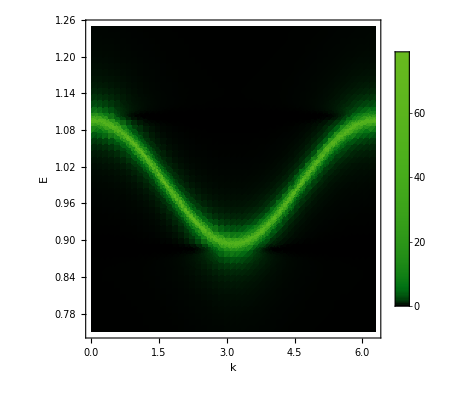

```mathematica
DensityPlot[-1/Pi Im[Gfinall],{k,0,2*Pi}, {z,0.75,1.25},AxesLabel->{"k","E"}, Exclusions->None, PlotLegends->Automatic, ColorFunction->(ColorData["AvocadoColors"][Log[1+#]/Log[2000]]&), ColorFunctionScaling->False, PlotRange->All,PlotPoints->50]
```